```mathematica
(*основные ошибки в определени функций*)
```

```mathematica
x= 2;
```

```mathematica
f1[x_]:=x^2 (*верно*)
```

```mathematica
f2[x]:= x^2
```

```mathematica
f3[x_]=x^2
```

4

```mathematica
f4[x]=x^2
```

4

```mathematica
f1[1]
```

1

```mathematica
f2[1]
```

f2[1]

```mathematica
f3[1]
```

4

```mathematica
f4[1]
```

f4[1]

```mathematica
Clear[x]
```

```mathematica
(*формула тейлора*)
```

```mathematica
f[x_]:=Cos[x]
```

```mathematica
Clear[x]
```

```mathematica
g=Series[f[x], {x, 0,3}]
```

1-x^2/2+O[x]^4

```mathematica
taylor[n_Integer]:= Series[f[x], {x, 0, n}]//Normal
```

```mathematica
taylor[5]
```

1-x^2/2+x^4/24

```mathematica
Manipulate[{Plot[Evaluate[{taylor[n], f[x]}],{x, -5,5}, PlotLegends->{"taylor", "function"}, PlotRange->{-1.5, 1.5}], taylor[n]}, {n, 1,10,1}]
```

```mathematica
Animate[{Plot[Evaluate[{taylor[n], f[x]}],{x, -5,5}, PlotLegends->{"taylor", "function"}, PlotRange->{-1.5, 1.5}], taylor[n]}, {n, 1,10,1}]
```

```mathematica
Animate[
Grid[
{{Plot[Evaluate[{taylor[n], f[x]}],{x, -5,5}, PlotLegends->{"taylor", "function"},
 PlotRange->{-1.5, 1.5}]}, {"Taylor=",taylor[n]}}], {n, 1,10,1}]
```

```mathematica
(*суммы и ряды*)
```

```mathematica
Sum[1/2^k, {k, 1, ∞}]
```

1

```mathematica
Sum[1/2^k, {k, 1, 10}]
```

1023/1024

```mathematica
SumConvergence[1/2^k,k]
```

True

```mathematica
SumConvergence[1/n, n]
```

False

```mathematica
SumConvergence[1/n^a, n]
```

Re[a]>1

```mathematica
Refine[%, Assumptions->a ∈Reals]
```

a>1

```mathematica
(*исследование функций*)
```

```mathematica
f[x_]:=x Exp[-x]
```

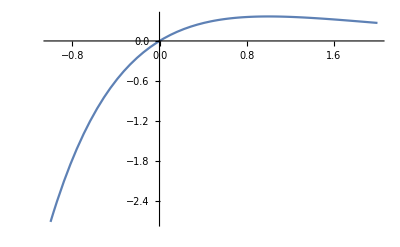

```mathematica
Plot[f[x], {x, -1,2}]
```

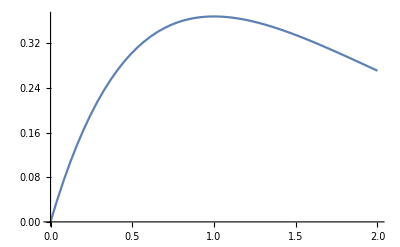

```mathematica
Plot[f[x], {x, 0,2}]
```

```mathematica
*-Graphics-
```

```mathematica
(*локальный экстремум*)
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→1}}

```mathematica
FindMaximum[f[x], {x,0.8}]
```

{0.367879,{x→1.}}

```mathematica
FindMinimum[f[x], {x,0.8}]
```

General::ovfl: Overflow occurred in computation.

FindMinimum::nrnum: The function value Overflow[] is not a real number at {x} = {-6.91145×10^15}.

{-1.433740734531271915875893104703881781684112055`15.954589770191005*^272873025596888,{x→-6.28313×10^14}}

```mathematica
(*наибольшее и наименошее значения функции на заданом отрезке*)
```

```mathematica
Maximize[{f[x],-1≤x≤2},x]
```

{1/ⅇ,{x→1}}

```mathematica
Minimize[{f[x],-1≤x≤2},x]
```

{-ⅇ,{x→-1}}

```mathematica
NMaximize[{f[x],-1≤x≤2},x]
```

{0.367879,{x→1.}}

```mathematica
NMinimize[{f[x],-1≤x≤2},x]
```

{-2.71828,{x→-1.}}

```mathematica
(*на R*)
```

```mathematica
Maximize[f[x],x]
```

{1/ⅇ,{x→1}}

```mathematica
Minimize[f[x],x]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{x→-∞}}

```mathematica
(*правила и подстановки*)
```

```mathematica
(*x->1 --Правило (Rule)*)
```

```mathematica
(*зачменить x на 1*)
```

```mathematica
2x+3/.x->1
```

5

```mathematica
(*/. - применение правила *)
```

```mathematica
s = Solve[2x+3==0, x]
```

{{x→-3/2}}

```mathematica
x^2+x/.s[[1]]
```

3/4

```mathematica
x+ y/. {x->1, y->-1}
```

0

```mathematica
x+ y/.x->1/. y->-1
```

0

```mathematica
(*Визуализация функций*)
```

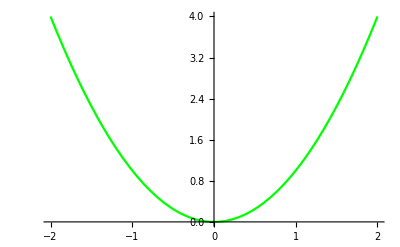

```mathematica
h1=Plot[x^2, {x,-2,2}, PlotStyle->{Green}]
```

```mathematica
(*неявно заданная функция *)
```

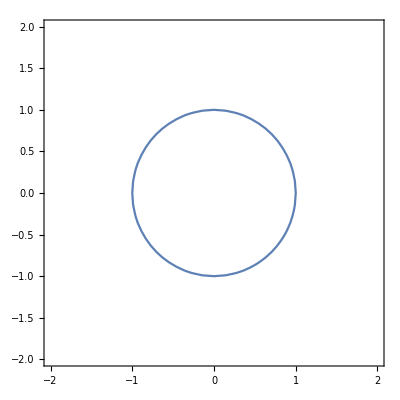

```mathematica
h2 = ContourPlot[x^2+y^2==1, {x,-2,2}, {y, -2, 2}]
```

```mathematica
(*параметрически заданная функция*)
```

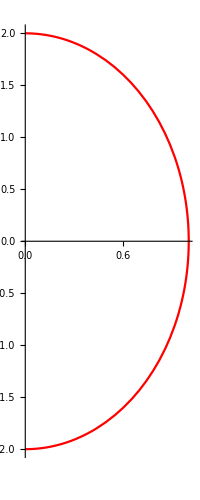

```mathematica
h3=ParametricPlot[{Sin[t], 2Cos[t]}, {t, 0 , π}, PlotStyle->{Red}]
```

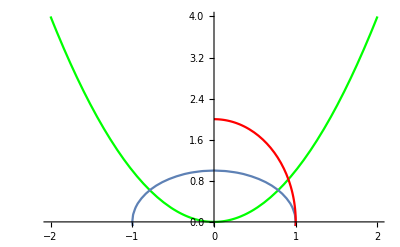

```mathematica
Show[h1,h2,h3]
```

```mathematica
(*полярная система координат*)
```

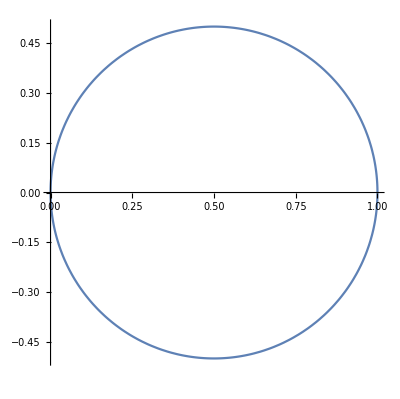

```mathematica
PolarPlot[Cos[ϕ], {ϕ, 0, π}]
```

```mathematica
(*Двумерная графика*)
```

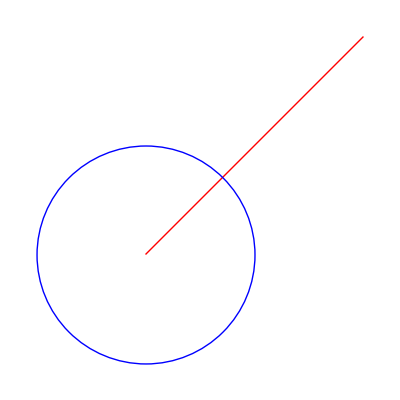

```mathematica
hp = Graphics[{Red, Line[{{0,0}, {2,2}}], Blue, Circle[{0,0},1]}]
```

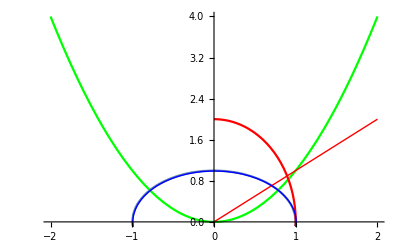

```mathematica
Show[h1,h2,h3,hp]
```

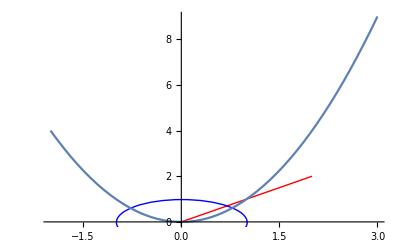

```mathematica
Plot[x^2, {x,-2,3}, Prolog->{Red, Line[{{0,0}, {2,2}}], Blue, Circle[{0,0},1]}]
```